## Singlet and triplet potentials from LeRoy code:

```mathematica
HartreePerMHz=6.579683920502 10^9;
```

Change these next commands to read your local files for the singlet and triplet potentials:

```mathematica
singletdata=Import["~/Documents/GitHub/LiScattering/fort.10"];
tripletdata=Import["~/Documents/GitHub/LiScattering/fort.30"];
rmin=singletdata[[1,1]];
rmax = singletdata[[Length[singletdata],1]];
```

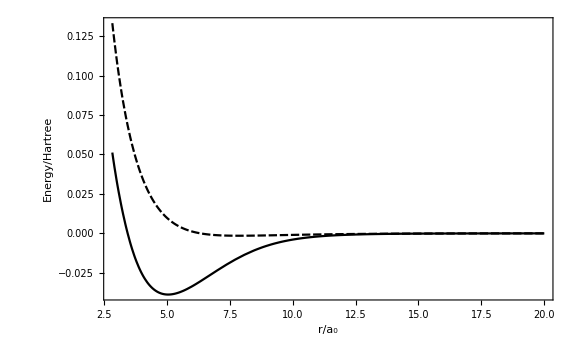

```mathematica
VSinglet = Interpolation[singletdata];
VTriplet = Interpolation[tripletdata];
Plot[{VSinglet[r],VTriplet[r]},{r,rmin,20},Frame->True,(*PlotRange->{-0.040,0.010}*)PlotRange->All,ImageSize->Large,FrameLabel->{"r/a_0","Energy/Hartree"},LabelStyle->Large]
```

Specify a Schrödinger operator with parameter h and potential V:

## Singlet/Triplet bound states (single-channel)

```mathematica
amu=(1.66053906660 10^-27)/(9.1093837015 10^-31)
```

1822.89

```mathematica
μ=(1 amu 7.01600455000)/2;
DeTriplet=333.758  4.55633525291208 10^-6;
DeSinglet=8516.709 4.55633525291208 10^-6;
ℒt=-1/(2 μ)u''[x]+(VTriplet[x]+DeTriplet)*u[x];
```

Find the 20 smallest eigenvalues and eigenfunctions on a refined mesh:

```mathematica
{valsTriplet,funsTriplet}=NDEigensystem[ℒt,u[x],{x,rmin,rmax},20, Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.001}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix «1» in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
valsTriplet-DeTriplet
```

{-0.0013753,-0.00110831,-0.000871097,-0.000662833,-0.000483149,-0.000332044,-0.000209777,-0.000116669,-0.0000526425,-0.0000161032,-1.89846×10^-6,1.36714×10^-7,3.58603×10^-7,7.99686×10^-7,1.3577×10^-6,2.50175×10^-6,2.9989×10^-6,4.40799×10^-6,5.85077×10^-6,7.04864×10^-6}

Visualize the eigenfunctions scaled by h and offset by the respective eigenvalue:

```mathematica
pvt=Plot[VTriplet[x],{x,rmin,rmax},PlotRange->{-DeTriplet,0.001}];
p1=Plot[(Evaluate[.0001funsTriplet[[11;;11]]+valsTriplet[[11;;11]]-DeTriplet]),{x,rmin,rmax},PlotRange->All,PlotStyle->Red];
```

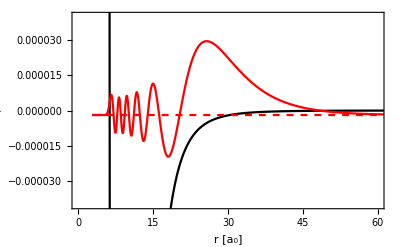

```mathematica
Show[{pvt,p1,Plot[valsTriplet[[11]]-DeTriplet,{x,rmin,rmax},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{0,60},{-0.00004,0.00004}},FrameLabel->{"r [a_0]","V_triplet"}]
```

```mathematica
ℒs=-1/(2 μ)u''[x]+(VSinglet[x]+DeSinglet)*u[x];
```

```mathematica
{valsSinglet,funsSinglet}=NDEigensystem[ℒs,u[x],{x,rmin,rmax},50,Method->{"SpatialDiscretization"->{"FiniteElement",{"MeshOptions"->{MaxCellMeasure->0.0001}}}}];
```

Eigensystem::maxit2: Warning: maximum number of iterations, 1000, has been reached by the Arnoldi algorithm without convergence to the specified tolerance, but the current best computed value has been returned. You can use method options with Method -> {Arnoldi, opts} to increase the size of basis vectors, the maximum number of iterations, reduce the tolerance, or use an estimate as a shift, any of which may help.

Eigensystem::chnpdef: Warning: there is a possibility that the second matrix SparseArray[Automatic,«1»,«3»,{1,{{«1»},{«1»}},{0.0000133333,-3.33333×10^-6,«14891045»,6.66666×10^-6,0.0000533333}}] in the first argument is not positive definite, which is necessary for the Arnoldi method to give accurate results.

```mathematica
valsSinglet-DeSinglet
```

{-0.0380075,-0.03643,-0.0348763,-0.0333466,-0.0318411,-0.0303601,-0.0289038,-0.0274725,-0.0260666,-0.0246865,-0.0233325,-0.0220052,-0.0207051,-0.0194327,-0.0181887,-0.0169737,-0.0157885,-0.014634,-0.013511,-0.0124206,-0.0113638,-0.0103419,-0.00935611,-0.00840795,-0.00749897,-0.00663089,-0.00580557,-0.00502506,-0.00429156,-0.00360748,-0.0029754,-0.00239807,-0.00187838,-0.00141933,-0.00102384,-0.000694537,-0.000433317,-0.000240368,-0.000112451,-0.0000404707,-7.73955×10^-6,6.22088×10^-6,0.0000272767,0.0000574498,0.000100942,0.000132881,0.000186305,0.000240224,0.000301443,0.000364063}

```mathematica
valsSinglet[[1;;41]]-DeSinglet
```

{-0.0380075,-0.03643,-0.0348763,-0.0333466,-0.0318411,-0.0303601,-0.0289038,-0.0274725,-0.0260666,-0.0246865,-0.0233325,-0.0220052,-0.0207051,-0.0194327,-0.0181887,-0.0169737,-0.0157885,-0.014634,-0.013511,-0.0124206,-0.0113638,-0.0103419,-0.00935611,-0.00840795,-0.00749897,-0.00663089,-0.00580557,-0.00502506,-0.00429156,-0.00360748,-0.0029754,-0.00239807,-0.00187838,-0.00141933,-0.00102384,-0.000694537,-0.000433317,-0.000240368,-0.000112451,-0.0000404707,-7.73955×10^-6}

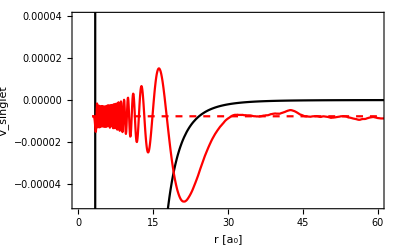

```mathematica
pvs=Plot[VSinglet[x],{x,rmin,rmax},PlotRange->{-DeSinglet,0.001}];
p2=Plot[(Evaluate[.0001funsSinglet[[41;;41]]+valsSinglet[[41;;41]]-DeSinglet]),{x,rmin,rmax},PlotRange->All,PlotStyle->Red];
Show[{pvs,p2,Plot[valsSinglet[[41]]-DeSinglet,{x,rmin,rmax},PlotStyle->{Dashed,Red}]},Axes->False, Frame->True, FrameStyle->Large,PlotRange->{{0,60},{-0.00005,0.00004}},FrameLabel->{"r [a_0]","V_singlet"}]
```

Okay well, the Le Roy potential gives the correct number of bound states in the singlet and triplet potentials.  41 in the singlet, and 11 in the triplet.

## Scattering lengths

```mathematica
Εtest=10^-16;sol=NDSolve[{-1/(2μ)u''[r]+VTriplet[r]u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
```

```mathematica
Plot[u[r]/.sol,{r,rmin,rmax}]
```

-Graphics-

```mathematica
CalcCotanDeltaTriplet[μ_,Εtest_,rmin_,rmax_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2},
r1=0.95 rmax;
r2=0.99rmax;

k=√(2 μ Εtest);
sol=NDSolve[{-1/(2μ)u''[r]+VTriplet[r]u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]
```

This module calculates the first two parameters in the effective range expansion

```mathematica
CalcERET[μ_,rmin_,rmax_,Εmin_,Εmax_]:=
Module[{vlocal,EREData,ascat,reff,A,B,fitpars,dE},
dE=(Εmax-Εmin)/10;
EREData=Table[{2μ Ε,√(2μ Ε)CalcCotanDeltaTriplet[μ,Ε,rmin,rmax]},{Ε,Εmin,Εmax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
Emin=10^-12;Emax=10^-11;{ascatT,reffT,EREDataT}=CalcERET[μ,rmin,rmax,10^-12,10^-11]
```

{-26.7233,441.809,{{1.27894×10^-8,0.0374234},{2.42998×10^-8,0.0374259},{3.58103×10^-8,0.0374285},{4.73208×10^-8,0.037431},{5.88312×10^-8,0.0374336},{7.03417×10^-8,0.0374361},{8.18521×10^-8,0.0374386},{9.33626×10^-8,0.0374412},{1.04873×10^-7,0.0374437},{1.16383×10^-7,0.0374463},{1.27894×10^-7,0.0374488}}}

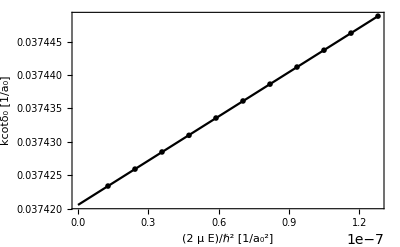

```mathematica
Show[ListPlot[EREData],Plot[-1/ascat+1/2 reff ksqr,{ksqr,0,2μ Emax}],PlotRange->All,Frame->True,LabelStyle->{12},FrameLabel->{"(2  μ Ε)/ℏ^2 [1/a_0^2]","kcotδ_0 [1/a_0]"}]
```

```mathematica
CalcCotanDeltaSinglet[μ_,Εtest_,rmin_,rmax_]:=
Module[{CotanDelta,sol,k,u1,u2,r1,r2},
r1=0.95 rmax;
r2=0.99rmax;

k=√(2 μ Εtest);
sol=NDSolve[{-1/(2μ)u''[r]+VSinglet[r]u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
u1=u[r1]/.sol[[1]];
u2=u[r2]/.sol[[1]];
CotanDelta=(-u2 Cos[k r1]+u1 Cos[k r2])/(u2 Sin[k r1]-u1 Sin[k r2]);
Return[CotanDelta]
]
```

```mathematica
CalcERES[μ_,rmin_,rmax_,Εmin_,Εmax_]:=
Module[{vlocal,EREData,ascat,reff,A,B,fitpars,dE},
dE=(Εmax-Εmin)/10;
EREData=Table[{2μ Ε,√(2μ Ε)CalcCotanDeltaSinglet[μ,Ε,rmin,rmax]},{Ε,Εmin,Εmax,dE}];
fitpars=FindFit[EREData,A+B ksqr,{A,B},ksqr];
ascat=-1/A/.fitpars;
reff=2B/.fitpars;
Return[{ascat,reff,EREData}]
]
```

```mathematica
Emin=10^-12;Emax=10^-11;{ascatS,reffS,EREDataS}=CalcERES[μ,rmin,rmax,10^-12,10^-11]
```

{34.9312,37.2661,{{1.27894×10^-8,-0.0286275},{2.42998×10^-8,-0.0286272},{3.58103×10^-8,-0.028627},{4.73208×10^-8,-0.0286268},{5.88312×10^-8,-0.0286266},{7.03417×10^-8,-0.0286264},{8.18521×10^-8,-0.0286262},{9.33626×10^-8,-0.028626},{1.04873×10^-7,-0.0286257},{1.16383×10^-7,-0.0286255},{1.27894×10^-7,-0.0286253}}}

```mathematica
Εtest=10^-16;sol=NDSolve[{-1/(2μ)u''[r]+VSinglet[r]u[r]==Εtest u[r],u[rmin]==0,u'[rmin]==10^-10},u,{r,rmin,rmax}];
Plot[u[r]/.sol,{r,rmin,rmax}]
```

-Graphics-